```mathematica
(* Load the necessary files *)
Get["/Users/devynmiller/Downloads/CHAPMAN MSBCE/SP 24/finance/Lags/ARlags.m"];
Get["/Users/devynmiller/Downloads/CHAPMAN MSBCE/SP 24/finance/Problem Set 2/BRLpCADpGBPpJPYpMXNpNOKpTRLpUSD.txt"];

(* Disable the underflow messages *)
Off[General::munfl];
```

# PROBLEM 8 FROM FIRST SET OF LECTURE NOTES

```mathematica
CADpUSDxUSDpGBP=N[Transpose[{Transpose[CADpUSD][[1]],Table[Transpose[CADpUSD][[2]][[i]]*Transpose[USDpGBP][[2]][[i]],{i,1,Length[CADpUSD]}]}]];
```

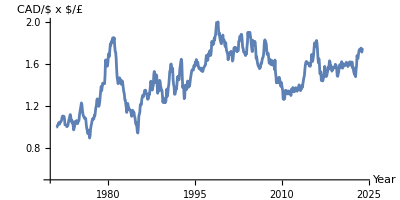

```mathematica
ListPlot[CADpUSDxUSDpGBP,PlotRange->{{1970,2024},{0.5,2}},Joined->True,AxesOrigin->{1970,0.5},AxesLabel->{"Year","CAD/$ x $/£"},AspectRatio->0.5]
```

```mathematica
LagTestAutomated[Transpose[CADpUSDxUSDpGBP][[2]],5,0.01]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0216811 | 0.00824897 | 2.62834 | 0.00878887
a | 0.0141405 | 0.00554062 | 2.55215 | 0.0109401
b1 | 0.233327 | 0.0386029 | 6.04427 | 2.5658×10^-9,0.0614561,1.53326}

```mathematica
(** An AR model is a type of time series model that uses past data points to predict future values.It assumes that past values have a linear influence on future values
I loaded the exchange rate data for CAD/USD and USD/GBP.This data is necessary to construct the CAD/GBP exchange rate through multiplication of the two rates.
Using the collected data,we constructed the CADpUSDxUSDpGBP series by multiplying the CAD/USD exchange rate by the USD/GBP exchange rate for each corresponding time period.
I then estimated the autoregressive model with lags for the newly constructed CADpUSDxUSDpGBP series.I used the LagTestAutomated function in Mathematica,specifying 5 lags and a significance level of 0.01.
The output from the LagTestAutomated function provided the estimates,standard errors,t-statistics,and p-values for the constant term and the first lag, using these results to understand the significance of the lags and the constant term in predicting the CAD/GBP exchange rate**)

(** The following are the values that could be added for a CADpUSDxUSDpGBP series row in Table 6:

Estimate (ˆc):0.02168105556164411
t-statistic:2.6283351596474422
p-value:0.008788869418909273
βˆ1:0.23332654024192404
βˆ3:—
βˆ9:—
rˆ∗:0.0614561 **)
```

# PROBLEM 9 FROM FIRST SET OF LECTURE NOTES

```mathematica
(*Generate the JPYpNOK series by dividing JPYpUSD by NOKpUSD*)
JPYpNOK=Transpose[{Transpose[JPYpUSD][[1]],Table[Transpose[JPYpUSD][[2]][[i]]/Transpose[NOKpUSD][[2]][[i]],{i,1,Length[JPYpUSD]}]}];

(*Perform the lag test estimation on the JPYpNOK series*)
LagTestAutomated[Transpose[JPYpNOK][[2]],5,0.01]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.148519 | 0.0544336 | 2.72843 | 0.00654055
a | 0.0126884 | 0.00424453 | 2.98935 | 0.00290432
b1 | 0.270304 | 0.0380264 | 7.10832 | 3.18424×10^-12,0.0861396,11.7051}

```mathematica
(** First,I needed the exchange rate data for JPY/USD and NOK/USD to calculate the JPY/NOK exchange rate.I created the JPYpNOK series by dividing the JPY/USD exchange rate by the NOK/USD exchange rate.This was done for each time period,which gave the JPY/NOK exchange rate series.Model Next,I estimated an autoregressive (AR) model with lags for the newly constructed JPYpNOK series.using LagTestAutomated.I specified 5 lags and set the significance level at 0.01,which means any lag with a p-value below 0.01 would be considered significant.The LagTestAutomated function gave the output,which included estimates,standard errors,t-statistics,and p-values for the constant term and the first lag.From this output,we can see which lags are significant and how they contribute to predicting the future values of the JPY/NOK exchange rate. **)
```

```mathematica
(** The following are the values that could be added for a JPYpNOK series row in Table 6:
Estimate (ˆc):0.14851851987532105
t-statistic:2.728433186658347
p-value:0.006540548806543249
β̂1:0.270303856637404
β̂3:—
β̂9:—
r̂*:0.0861396 **)
```

```mathematica
y[p_,x0_,y0_,pi_,a_]:=(x0+p y0) ((1-pi)^(1/a))/((p pi)^(1/a)+p (1-pi)^(1/a));
yB[p_]:=y[p,24,2,5/12,2];
yS[p_]:=y[p,2,18,5/12,2];
Z[p_]:=yB[p]-2+yS[p]-18;
```

```mathematica
(*Initialize variables*)
p0=4;
alpha=0.1;
prices={p0};
excessDemands={Z[p0]};
iterations=35; (*Number of iterations for alpha=0.1*)
```

```mathematica
(*Iterative process to adjust prices*)
Do[pNew=Last[prices]+alpha Z[Last[prices]];
AppendTo[prices,pNew];
AppendTo[excessDemands,Z[pNew]];,{iterations}];
```

```mathematica
(*Verify the price sequence*)
prices
excessDemands
```

{4,3.86282,3.73209,3.60805,3.4909,3.38081,3.27788,3.18214,3.0936,3.01215,2.93767,2.86992,2.80866,2.75356,2.70427,2.66039,2.62151,2.58723,2.55712,2.53077,2.5078,2.48784,2.47054,2.45558,2.44268,2.43158,2.42203,2.41384,2.40683,2.40082,2.39568,2.39129,2.38754,2.38435,2.38162,2.37929}

{-20+(53 √(7/3))/(√(5/3)+2 √(7/3)),-1.30731,-1.24038,-1.17144,-1.10092,-1.02936,-0.957333,-0.885473,-0.814434,-0.744868,-0.677403,-0.612612,-0.550997,-0.492963,-0.438814,-0.388745,-0.342847,-0.30111,-0.263444,-0.229688,-0.199626,-0.173009,-0.149564,-0.129007,-0.111057,-0.0954399,-0.0818954,-0.070181,-0.0600739,-0.0513718,-0.043893,-0.0374757,-0.0319765,-0.0272695,-0.0232447,-0.0198061}

```mathematica
(*Now adjust the price path with alpha=0.02*)
alpha=0.02;
pricesAlpha002={p0};
excessDemandsAlpha002={Z[p0]};
iterationsAlpha002=175; (*Number of iterations for alpha=0.02*)

Do[pNew=Last[pricesAlpha002]+alpha Z[Last[pricesAlpha002]];
AppendTo[pricesAlpha002,pNew];
AppendTo[excessDemandsAlpha002,Z[pNew]];,{iterationsAlpha002}];
```

```mathematica
(*Output the new price path*)
pricesAlpha002
excessDemandsAlpha002
```

{4,3.97256,3.94538,3.91844,3.89176,3.86533,3.83916,3.81325,3.78759,3.76221,3.73708,3.71222,3.68762,3.6633,3.63924,3.61546,3.59194,3.5687,3.54573,3.52304,3.50062,3.47848,3.45662,3.43504,3.41373,3.39271,3.37196,3.35149,3.3313,3.3114,3.29177,3.27242,3.25335,3.23457,3.21606,3.19783,3.17988,3.1622,3.1448,3.12768,3.11084,3.09426,3.07796,3.06194,3.04618,3.03069,3.01547,3.00051,2.98582,2.97139,2.95722,2.94331,2.92966,2.91626,2.90312,2.89022,2.87757,2.86517,2.85301,2.84109,2.82941,2.81797,2.80676,2.79578,2.78503,2.7745,2.76419,2.7541,2.74423,2.73458,2.72513,2.71589,2.70685,2.69802,2.68938,2.68094,2.67269,2.66463,2.65676,2.64907,2.64156,2.63423,2.62707,2.62008,2.61325,2.60659,2.6001,2.59376,2.58758,2.58155,2.57566,2.56993,2.56434,2.55889,2.55357,2.54839,2.54335,2.53843,2.53364,2.52897,2.52442,2.51999,2.51568,2.51148,2.50739,2.50341,2.49953,2.49576,2.49209,2.48851,2.48503,2.48165,2.47836,2.47515,2.47204,2.469,2.46605,2.46319,2.4604,2.45768,2.45504,2.45248,2.44999,2.44756,2.4452,2.44291,2.44068,2.43852,2.43641,2.43437,2.43238,2.43045,2.42857,2.42675,2.42498,2.42326,2.42158,2.41996,2.41838,2.41685,2.41536,2.41391,2.4125,2.41114,2.40981,2.40852,2.40727,2.40606,2.40488,2.40373,2.40262,2.40154,2.40049,2.39948,2.39849,2.39753,2.3966,2.39569,2.39481,2.39396,2.39313,2.39233,2.39155,2.39079,2.39006,2.38934,2.38865,2.38798,2.38733,2.38669,2.38608,2.38548,2.3849,2.38434,2.3838,2.38327}

{-20+(53 √(7/3))/(√(5/3)+2 √(7/3)),-1.35937,-1.3468,-1.33414,-1.32138,-1.30854,-1.2956,-1.28258,-1.26948,-1.2563,-1.24304,-1.22971,-1.21631,-1.20284,-1.18931,-1.17571,-1.16206,-1.14836,-1.13461,-1.12082,-1.10699,-1.09311,-1.07921,-1.06528,-1.05133,-1.03735,-1.02337,-1.00937,-0.995364,-0.98136,-0.96736,-0.953369,-0.939392,-0.925432,-0.911496,-0.897588,-0.883712,-0.869873,-0.856077,-0.842327,-0.828629,-0.814988,-0.801407,-0.787892,-0.774447,-0.761076,-0.747784,-0.734575,-0.721454,-0.708423,-0.695489,-0.682654,-0.669922,-0.657297,-0.644782,-0.632382,-0.620099,-0.607936,-0.595897,-0.583984,-0.572201,-0.56055,-0.549033,-0.537653,-0.526412,-0.515312,-0.504356,-0.493544,-0.482878,-0.472361,-0.461992,-0.451774,-0.441708,-0.431793,-0.422032,-0.412424,-0.402971,-0.393672,-0.384527,-0.375537,-0.366702,-0.358021,-0.349495,-0.341122,-0.332902,-0.324835,-0.31692,-0.309156,-0.301542,-0.294077,-0.28676,-0.27959,-0.272565,-0.265685,-0.258947,-0.252351,-0.245895,-0.239577,-0.233396,-0.227349,-0.221436,-0.215655,-0.210003,-0.204479,-0.199081,-0.193807,-0.188655,-0.183623,-0.17871,-0.173913,-0.169231,-0.164661,-0.160201,-0.15585,-0.151605,-0.147465,-0.143427,-0.13949,-0.135652,-0.131909,-0.128262,-0.124707,-0.121244,-0.117869,-0.114581,-0.111378,-0.108258,-0.10522,-0.102262,-0.0993813,-0.0965769,-0.093847,-0.0911897,-0.0886034,-0.0860864,-0.0836372,-0.081254,-0.0789353,-0.0766796,-0.0744853,-0.0723509,-0.070275,-0.0682561,-0.0662927,-0.0643835,-0.0625272,-0.0607223,-0.0589676,-0.0572617,-0.0556035,-0.0539917,-0.052425,-0.0509024,-0.0494226,-0.0479846,-0.0465871,-0.0452293,-0.0439099,-0.0426279,-0.0413825,-0.0401725,-0.038997,-0.0378551,-0.0367459,-0.0356684,-0.0346219,-0.0336054,-0.0326182,-0.0316594,-0.0307282,-0.0298239,-0.0289458,-0.0280931,-0.027265,-0.026461,-0.0256803}

# MY ANSWER TO PROBLEM 6 FOR SECOND SET OF LECTURE NOTES BEGINS UNDER THE TITLE "PROBLEM 6 SOLUTION"

```mathematica
(*  DEMAND FOR GOOD Y       *)
```

```mathematica
y[p_, x0_, y0_, pi_, a_]:= ((x0 + p y0)*(1 - pi)^(1/a))/((p * pi)^(1/a) +p(1 - pi)^(1/a))
```

```mathematica
y[4, 2, 18, 0.4167, 2]
```

13.0043

```mathematica
yB[p_]:= (24 + 2 p) 7^0.5/((5 p)^0.5 + p 7^0.5)
```

```mathematica
yB[4]
```

5.6236

```mathematica
yS[p_]:= (2 + 18 p) 7^0.5/((5 p)^0.5 + p 7^0.5)
```

```mathematica
yS[4]
```

13.0046

```mathematica
(*  AN EQUIVALENT EXPRESSION FOR DEMAND     *)
```

```mathematica
A[p_, pi_, a_]:= (p * pi/(1 - pi))^(1/a)
```

```mathematica
Y[p_, x0_, y0_, pi_, a_]:= (x0 + p y0)/(A[p, pi, a] +p)
```

```mathematica
{Y[2.36, 2, 18, 5/12, 2], N[Y[4, 24, 2, 5/12, 2]]}
```

{12.1585,5.6236}

```mathematica
(*  EXCESS DEMAND IS THE CHANGE BETWEEN THE FINAL DEMAND FOR Y AND   *)
(*  THE AGENT'S ENDOWMENT OF Y.                                      *)
```

```mathematica
Z[p_, x0_, y0_, pi_, a_]:= Y[p, x0, y0, pi, a] - y0
```

```mathematica
{Z[2.366, 2, 18, 5/12, 2], Z[2.366, 24, 2, 5/12, 2]}
```

{-5.83742,5.83742}

```mathematica
Z[p_]:= Z[p, 2, 18, 5/12, 2] + Z[p, 24, 2, 5/12, 2]
```

```mathematica
N[Z[4]]
```

-1.37184

```mathematica
(*  The next several steps modify the ticks and tick labels on the   *)
(*  excess demand graph to move them above the horizontal axis.      *)
(*  I did this so that the dotted lines for the excess demand        *)
(*  would not run through the axis label at p = 4.                   *)
```

```mathematica
plt = Plot[Z[p], {p, 0.01, 6}, PlotRange -> {{0, 5}, {-2, 6}}, AxesLabel-> {"p", "Z(p)"},LabelStyle->{FontSize->11,Black}];
```

```mathematica
tks=AbsoluteOptions[plt,Ticks];
```

```mathematica
xTks=Map[If[Head[#[[2]]]===Real,ReplacePart[#,{"",{.01,0}},{{2},{3}},{{1},{2}}],#]&,tks[[1,2,1]]];
```

```mathematica
tklbls = Table[Style[Text[i, {i, 0.35}], FontSize->11],{i,1,5}];
```

```mathematica
(*  This graph shows the excess demand function and it emphasizes    *)
(*  the magnitude of excess demand at p = 4 with dotted lines.       *)
```

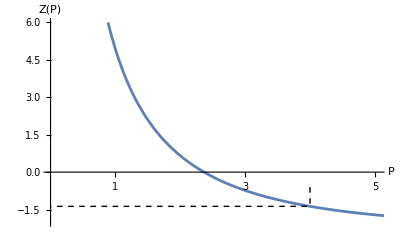

```mathematica
Show[Plot[Z[p], {p, 0.01, 6}, Ticks -> {{1, 2, 3, 4, 5, 6}, Automatic}, PlotRange -> {{0, 5.04}, {-2, 6}}, AxesLabel-> {"P", "Z(P)"},LabelStyle->{FontSize->11,Black}], Graphics[{Dashing[{0.01, 0.01, 0.01}], Line[{{4, -0.6}, {4, -1.37222}, {0, -1.37222}}]}]]
```

```mathematica
(*  If the market excess demand is set equal to zero the equilibrium    *)
(*  price can be determined with a little bit of algebra.  It is        *)
(*  p* = 1.3^2 * 1.4.                                                  *)
```

```mathematica
1.3 * 1.3 * 1.4
```

2.366

```mathematica
Z[2.366]
```

-8.88178×10^-16

```mathematica
(*  We can use the adjustment equation (17) in the lecture notes to    *)
(*  model an iterative price adjustment process.                       *)
```

```mathematica
4 + 0.1 * Z[4]
```

3.86282

```mathematica
(*  Suppose that we define an adjustment process using the       *)
(*  excess demand function Z[p] by the equation                  *)
```

```mathematica
f[p_, a_]:= Join[p, {p[[-1]] + a  * Z[p[[-1]]]}]
```

```mathematica
(*  We can use f[p, a] to get a price path step-by-step.        *)
```

```mathematica
p1 = f[{4}, 0.1]
```

{4,3.86282}

```mathematica
p2 = f[p1, 0.1]
```

{4,3.86282,3.73209}

```mathematica
p3 = f[p2, 0.1]
```

{4,3.86282,3.73209,3.60805}

```mathematica
(*  Problem 6   *)
(*  Write a function that will iteratively determine prices like the    *)
(*  prices above.  Use the output above to verify that your function    *)
(*  works properly.  Then use your function to evaluate the price       *)
(*  path starting at p0 = 4 with an adjustment rate of 0.02 with 175    *)
(*  iterations.          *)
```

```mathematica
PriceSequence[p_, a_, n_]:= Module[{k, pNew, pTmp}, 
k = Length[p];
pTmp = p;
Label[start];
(*  Write some code here to make a function that generates prices  *)
(*  iteratively.  I was able to do this with 2 lines of code.      *)
k = k + 1;
If[k < n, Goto[start]];
Return[pTmp]]
```

```mathematica
PriceSequence[{4}, 0.1, 35]
```

{4}

```mathematica
PriceSequence[{4}, 0.02, 175]
```

{4}

```mathematica
(*  If we linearize the excess demand function at the equilbrium     *)
(*  we get a representation that is similar to an autoregressive     *)
(*  process.                                                         *)
```

```mathematica
Z'[2.366]
```

-1.49877

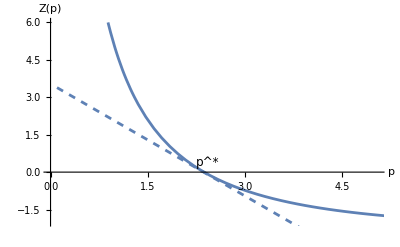

```mathematica
Show[Plot[Z[p], {p, 0.01, 6}, PlotRange -> {{0, 5.04}, {-2, 6}}, AxesLabel-> {"p", "Z(p)"},LabelStyle->{FontSize->11,Black}], 
Graphics[Text[StyleForm[Superscript["p", "*"],12],{2.42, 0.4}]], Plot[Z'[2.366] *(x - 2.36), {x, 0.1, 6}, PlotStyle -> Dashed]]
```

```mathematica
1/(2 - 2^0.5)
```

1.70711

# PROBLEM 6 SOLUTION

```mathematica
(**To create a function in Mathematica that iteratively determines prices based on the excess demand function Z[p]and an adjustment rate a,we can define a function that updates the price based on the previous price and the excess demand at that price.The function will use a loop to perform the updates for a specified number of iterations.**)
```

```mathematica
IterativePriceAdjustment[p0_,a_,iterations_]:=Module[{prices,i},prices={p0};(*Initialize the list of prices with the initial price*)For[i=1,i<=iterations,i++,AppendTo[prices,Last[prices]+a*Z[Last[prices]]]];
prices]
```

```mathematica
(**This function initializes a list of prices with the initial price p0.It then uses a 'for loop' to iteratively calculate new prices based on the last price in the list and the excess demand at that price,adjusted by the factor a.The new price is appended to the list of prices.After completing the specified number of iterations,the function returns the list of prices.**)
```

```mathematica
(*Verify the function with the initial conditions from the provided code*)initialTest=IterativePriceAdjustment[4,0.1,3]
```

{4,3.86282,3.73209,3.60805}

```mathematica
(**This should output {4,3.86282,3.73209,3.60805},matching the previous code.Now,to evaluate the price path starting at p0=4 with an adjustment rate of 0.02 and 175 iterations.
```

```mathematica
(*Calculate the price path with 175 iterations*)pricePath=IterativePriceAdjustment[4,0.02,175]
```

{4,3.97256,3.94538,3.91844,3.89176,3.86533,3.83916,3.81325,3.78759,3.76221,3.73708,3.71222,3.68762,3.6633,3.63924,3.61546,3.59194,3.5687,3.54573,3.52304,3.50062,3.47848,3.45662,3.43504,3.41373,3.39271,3.37196,3.35149,3.3313,3.3114,3.29177,3.27242,3.25335,3.23457,3.21606,3.19783,3.17988,3.1622,3.1448,3.12768,3.11084,3.09426,3.07796,3.06194,3.04618,3.03069,3.01547,3.00051,2.98582,2.97139,2.95722,2.94331,2.92966,2.91626,2.90312,2.89022,2.87757,2.86517,2.85301,2.84109,2.82941,2.81797,2.80676,2.79578,2.78503,2.7745,2.76419,2.7541,2.74423,2.73458,2.72513,2.71589,2.70685,2.69802,2.68938,2.68094,2.67269,2.66463,2.65676,2.64907,2.64156,2.63423,2.62707,2.62008,2.61325,2.60659,2.6001,2.59376,2.58758,2.58155,2.57566,2.56993,2.56434,2.55889,2.55357,2.54839,2.54335,2.53843,2.53364,2.52897,2.52442,2.51999,2.51568,2.51148,2.50739,2.50341,2.49953,2.49576,2.49209,2.48851,2.48503,2.48165,2.47836,2.47515,2.47204,2.469,2.46605,2.46319,2.4604,2.45768,2.45504,2.45248,2.44999,2.44756,2.4452,2.44291,2.44068,2.43852,2.43641,2.43437,2.43238,2.43045,2.42857,2.42675,2.42498,2.42326,2.42158,2.41996,2.41838,2.41685,2.41536,2.41391,2.4125,2.41114,2.40981,2.40852,2.40727,2.40606,2.40488,2.40373,2.40262,2.40154,2.40049,2.39948,2.39849,2.39753,2.3966,2.39569,2.39481,2.39396,2.39313,2.39233,2.39155,2.39079,2.39006,2.38934,2.38865,2.38798,2.38733,2.38669,2.38608,2.38548,2.3849,2.38434,2.3838,2.38327}